```mathematica
θlocal=0;
LogoSize=240;
logo=Rotate[Text[Style["L","Title",FontSize->LogoSize],{-1/12,-1/12} ,{0,0},{1,0}],θlocal,{-1/12,-1/12}]
```

Text[L,{-1/12,-1/12},{0,0},{1,0}]

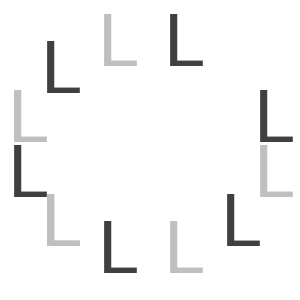

```mathematica
RotImages=6;
Graphics[{Table[{GrayLevel[1/2+0.5(1/2-Mod[r,2])],Rotate[logo,-Pi- r(2 Pi-Pi)/RotImages,{0,0}],Rotate[logo,Pi+r(2 Pi-Pi)/RotImages,{0,0}]},{r,1,RotImages}]},PlotRange->1,ImageSize->{300,300}]
```

```mathematica
Manipulate[
With[{i=Rotate[Text[Style[ToString[st],"Title",FontSize->f],xy ,{0,0},{1,0}],-pr,xy]},
Graphics[{Table[{GrayLevel[1/2+gr(1/2-Mod[r+bw,2])],Rotate[i,-ra- r(2 Pi-ra)/k,{0,0}],Rotate[i,ra+r(2 Pi-ra)/k,{0,0}]},{r,1,k}]},PlotRange->1,ImageSize->{300,300}]],
{{pr,0,"original rotation"},-Pi,Pi},{{k,6,"rotated pairs"},1,12,1},{{ra,Pi,"rotation limits"},0,2Pi},{{f,240,"size"},1,240,1,ImageSize->Tiny,ControlPlacement->Left},{{gr,1,"gray"},0,1,ImageSize->Tiny,ControlPlacement->Left},{{xy,{-1/12,-1/12},"translation"},{-1/4,-1/4},{1/4,1/4},ControlType->Locator,Appearance->None},{{bw,0,"inversion"},{0->"plain",1->"inverted"},ControlPlacement->Left},{{st,"L","text"},ControlType->None,ControlPlacement->Left}]
```

```mathematica
ℒℐ𝒩𝒱𝒜ℛℐ𝒜𝒩𝒯
```

ℒℐ𝒩𝒱𝒜ℛℐ𝒜𝒩𝒯